Thermal properties of the Steel 316L:
Type 316L in liquid and solid state:

```mathematica
Hs[T_]:= -34.127 + 0.1097 T + 1.587 10^-5 T^2;
Hl[T_] := 0.1840 T - 50.573;
```

Plot the enthalpy as function of temperature:

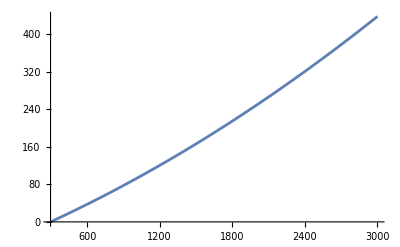

```mathematica
sp = Plot[Hs[T], {T,298, 3000}]
```

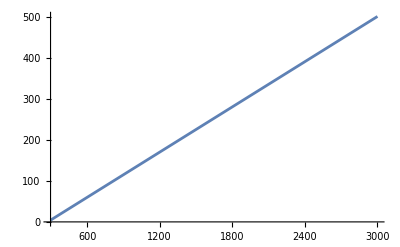

```mathematica
lp = Plot[Hl[T], {T,298,3000}]
```

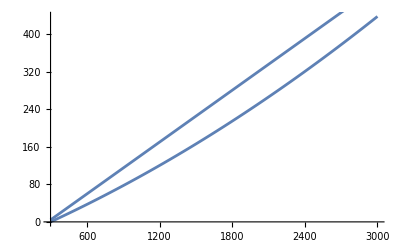

```mathematica
Show[{sp,lp}]
```

Create the piecewise function from liquid and solid regions:

```mathematica
Ht[T_]:= Piecewise[{{Hs[T],298<= T <= 1700},{Hl[T], T> 1700}}]
```

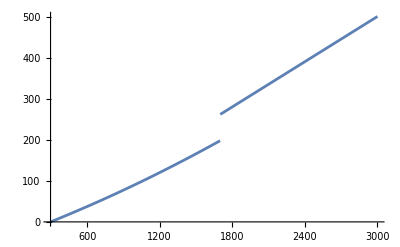

```mathematica
Plot[Ht[T], {T,298,3000}]
```

```mathematica
UnitConvert[Quantity[1.0, "Calories4C"/"Grams"], "Joules"/"Kilograms"]
```

4190. J/kg

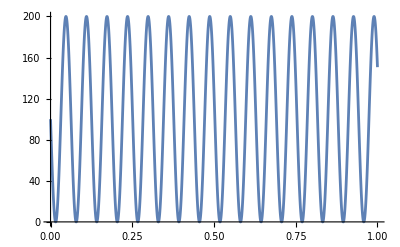

```mathematica
Plot[100*(1-Sin[1/0.01 t]), {t,0,1}]
```